## Hamiltonians

### Definitions

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(* Harper antiperiodic *)
hharpa[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*antiperiodic boundary conditions*)AppendTo[hopping,{1,q}->1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_]:=hharp[Fibonacci[n-2],Fibonacci[n-1]];
hfiba[n_]:=hharpa[Fibonacci[n-2],Fibonacci[n-1]];
```

## Averaged exponent of the local spectral measure

### Definitions

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBands[n_,ρ_]:=IntBands[n,ρ]=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];µ
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

(* we want to order wavefunctions by site rather than by energy *)
{Transpose[intensities],bands}]
```

```mathematica
(* averaged Γ^μ *)
avqInt[τ_,q_,n_,ρ_]:=avqInt[τ,q,n,ρ]=Total[(IntBands[n,ρ][[2]])^-τ Total[IntBands[n,ρ][[1]]^q]]/Fibonacci[n];
```

For large values of q, the 3-periodic behaviour of the Fibonacci numbers (odd, odd, even...) is clearly visible.
It impacts on the behaviour of Γ^n(q,τ) for τ fixed (not necessarily equal to τ_q).

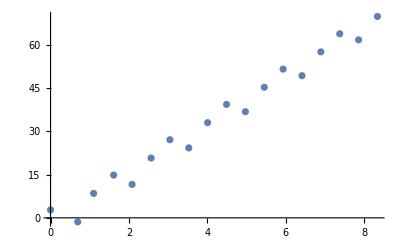

```mathematica
τ=3.;
nValues=Range[2,19,1];
avIntN=Map[avqInt[τ,10.,#,0.1]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

```mathematica
Clear[τ];
```

Because of the 3-periodicity, we compute Γ^n/Γ^(n-3) rather than Γ^n/Γ^(n-1).

```mathematica
tau[q_,n_,ρ_]:=τ/.FindRoot[avqInt[τ,q,n,ρ]/avqInt[τ,q,n-3,ρ]-1,{τ,0.}]
```

The computed value τ_q^n itself depends on n (mod 3). Again, chosing F_n odd and F_(n-2) as well makes more sense because the centre of the three main clusters is not gaped in the n → ∞ limit.

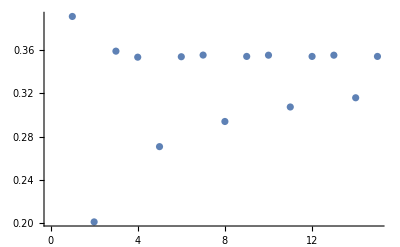

```mathematica
nValues=Range[5,19,1];
ListPlot[tau[10.,#,0.1]&/@nValues]
```

### Computations

```mathematica
nValue=19;
qValues=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5];
τaus=tau[#,nValue,0.1]&/@qValues;
dqs=τaus/(qValues-1);
```

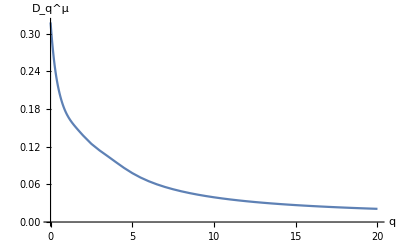

```mathematica
ListPlot[glue[qValues,dqs],Joined->True,AxesLabel->{"q","D_q^μ"}]
```

```mathematica
Export[NotebookDirectory[]<>"data/average_local_spectral_dimension_ρ_10.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/average_local_spectral_dimension_ρ_10.pdf

It is also possible to derive recursion relations on Γ_q^n using the second-order perturbation theory on wavefunctions:
Γ_q^n=2(λ/2)^q ω^2 z^-τ Γ_q^(n-2)+(λ')^q ω^3(z')^-τ Γ_q^(n-3)
with λ = 1/(1+ρ^2/2), λ'=1/(1+2 ρ^2).

Using that Γ_q^(n+1)/Γ_q^n~1, we arrive at an implicit equation on τ_q:

```mathematica
eq[q_,τq_,ρ_]:=2/((2+ρ^2)^q)ω^2(ρ/2)^-τq+1/((1+2 ρ^2)^q)ω^3 ρ^(-2τq)-1;
```

```mathematica
implicitTau[q_,ρ_]:=τ/.FindRoot[eq[q,τ,ρ],{τ,0.}]
```

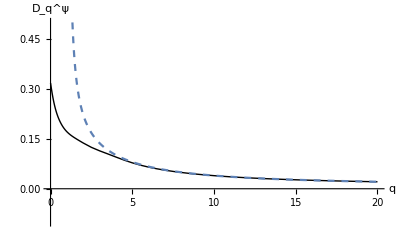

```mathematica
Plot[{implicitTau[q,0.1]/(q-1)},{q,1.15,20.},Prolog->{Thick,Line@glue[qValues,dqs]},PlotRange->{{0.,20},{-0.1,0.5}},AxesLabel->{"q","D_q^ψ"},PlotStyle->Dashed]
```

```mathematica
Export[NotebookDirectory[]<>"data/average_local_spectral_dimension_ρ_10.pdf",%]
```

/home/nicolas/git/spectrum_quasicrystals/Fibonacci/data/average_local_spectral_dimension_ρ_10.pdf

### Harper

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBandsHarp[n_]:=IntBands[n]=Block[{vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n]];
{vpa,wfa}=Eigensystem[hfiba[n]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

(* we want to order wavefunctions by site rather than by energy *)
{Transpose[intensities],bands}]
```

```mathematica
(* averaged Γ^μ *)
avqIntHarp[τ_,q_,n_]:=avqIntHarp[τ,q,n]=Total[(IntBandsHarp[n][[2]])^-τ Total[IntBandsHarp[n][[1]]^q]]/Fibonacci[n];
```

The 3-periodicity is also visible for the Harper model.

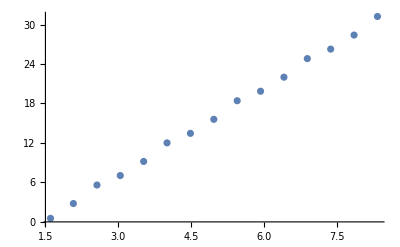

```mathematica
τ=3.;
nValues=Range[5,19,1];
avIntN=Map[avqIntHarp[τ,10.,#]&,nValues];
ListPlot[Log@glue[Fibonacci[nValues],avIntN]]
```

Because of the 3-periodicity, we compute Γ^n/Γ^(n-3) rather than Γ^n/Γ^(n-1).

```mathematica
tauHarp[q_,n_]:=τ/.FindRoot[avqIntHarp[τ,q,n]/avqIntHarp[τ,q,n-3]-1,{τ,0.}]
```

The computed value τ_q^n itself depends on n (mod 3). Again, chosing F_n odd and F_(n-2) as well makes more sense because the centre of the three main clusters is not gaped in the n → ∞ limit.

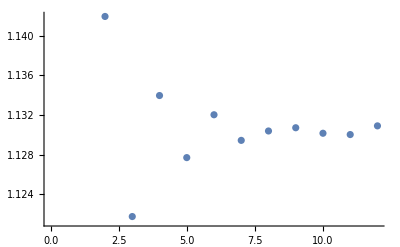

```mathematica
nValues=Range[8,19,1];
ListPlot[tauHarp[10.,#]&/@nValues]
```

```mathematica
nValue=19;
qValues=Range[0.,0.99,0.05]~Join~Range[1.01,2.,0.1]~Join~Range[2.,20.,0.5];
τausHarp=tauHarp[#,nValue]&/@qValues;
dqsHarp=τausHarp/(qValues-1);
```

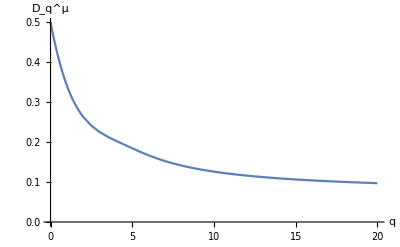

```mathematica
ListPlot[glue[qValues,dqsHarp],Joined->True,AxesLabel->{"q","D_q^μ"}]
```